```mathematica
SetDirectory[NotebookDirectory[]];
```

## Finding the Real Function Call Time (δT)

```mathematica
Clear[f]
```

0.00965379

```mathematica
fold[δt_]:=Module[{data},
data= Import[FileNameJoin[{NotebookDirectory[],"Func_Call/"<>ToString[δt]<>".dat"}], "CSV"];
Mean[data[[;;, 2]]]
]
```

```mathematica
f[δt_]:=Module[{data},Import[FileNameJoin[{NotebookDirectory[],"Func_Call/"<>δt<>".dat"}]]//Flatten//Mean]
```

```mathematica
Export["RealTime_vs_SleepTime.dat", Table[f[δt[[i]]], {i, 1, Length[δt]}],"Table"]
```

RealTime_vs_SleepTime.dat

```mathematica
RealTvsSleepT = Import[FileNameJoin[{NotebookDirectory[],"RealTime_vs_SleepTime.dat"}]]//Flatten ;
```

```mathematica
g :=Module[{},  
Table[f[δt],{δt, 0.001, 5-0.001, 0.001}]]
```

```mathematica
Flatten[g, 1]
```

{{1/1000,0.0111203},{1/500,0.0108571},{3/1000,0.0124045},{1/250,0.0131897},{1/200,0.0158088},{3/500,0.0158786},{7/1000,0.0175734},{1/125,0.0184273},{9/1000,0.0245385},{1/100,0.0351789},{1/50,0.0433525},{3/100,0.0529029},{1/25,0.0709866},{1/20,0.0878407},{3/50,0.100754},{7/100,0.113529},{2/25,0.125337},{9/100,0.140705},{1/10,0.150242},{1/5,0.274505},{3/10,0.389339},{2/5,0.516015},{1/2,0.63774},{3/5,0.785814},{7/10,0.915514},{4/5,1.0388},{9/10,1.17652},{1,1.30095},{2,2.49448},{3,3.71194},{4,4.85456},{5,5.95877},{6,7.05994},{7,8.06658},{8,8.98967},{9,9.93994}}

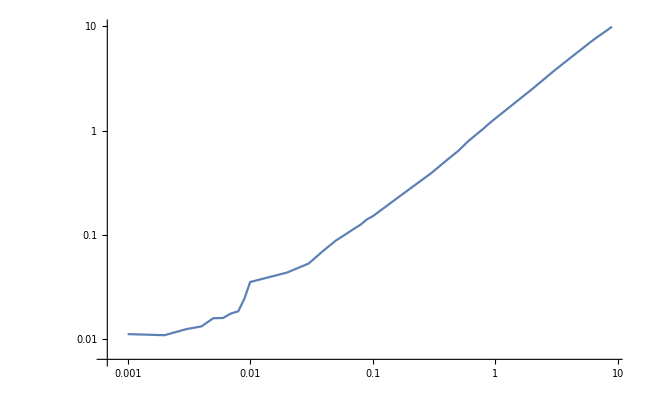

```mathematica
ListLogLogPlot[Flatten[g, 1], Joined->True]
```

```mathematica
ScientificForm[0.7845]
```

7.845×10^-1

## Parallel Mode (ΔT ~ 0 ms) (Sorted)

```mathematica
data1 = {{100,{1639.42,
 1112.11,
1096.76,
 1052.57,
1216.56,
1207.74,
 1332.28,
1355.67}},
{200,{5007.47,
6377.52,
6255.69,
6164.36,
6692.66,
6753.09,
6809.10,
6568.26}},
{300,{15775.66,
18650.51,
18052.32,
17945.01,
18547.71,
 18832.57,
19254.77,
 20236.73}}};
```

```mathematica
Clear[g]
```

```mathematica
f[res_, thread_, data_]:=data[[res]][[2]][[thread]]
```

```mathematica
g[thread_, data_]:=Table[{data[[i]][[1]], (f[i,thread, data]/f[i,1, data])^-1}, {i, 1, 3}]
```

```mathematica
Table[g[i, data1], {i, 1, 8}]
```

{{{100,1.},{200,1.},{300,1.}},{{100,1.47415},{200,0.785175},{300,0.845857}},{{100,1.49478},{200,0.800466},{300,0.873885}},{{100,1.55754},{200,0.812326},{300,0.879111}},{{100,1.34759},{200,0.748203},{300,0.850545}},{{100,1.35743},{200,0.741508},{300,0.83768}},{{100,1.23054},{200,0.735408},{300,0.819312}},{{100,1.20931},{200,0.762374},{300,0.779556}}}

```mathematica
f[1,2]
```

1112.11

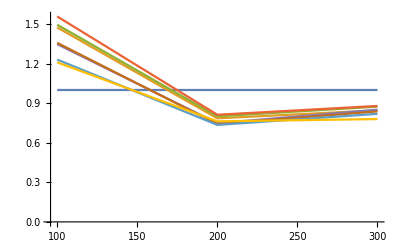

```mathematica
ListPlot[Table[g[i], {i, 1, 8}], Joined->True]
```

## Parallel Mode (ΔT = 1 ms) (Sorted)

## Parallel Mode (ΔT = 1 ms) (Not Sorted)

## Ludicrous Mode (ΔT = 1 ms) (Not Sorted)

```mathematica
data4= {{50,{4462.11,
50,1970.01,
50,1339.41,
50,1075.89,
50,955.20,
50,800.61,
50,687.54,
50, 617.96}},
{100,{14300.80,
100,7615.51,
100,5191.15,
100,4131.14,
100, 3450.37,
100,2883.62,
100,2564.48,
100, 2250.55}},
{150,{31787.42,
150, 16849.91,
150, 11544.59,
150, 8980.66,
150, 7465.01,
150,6500.16,
150, 5551.83,
150,4854.56}}};
```

```mathematica
Table[g[i, data4], {i, 1, 8}]
```

{{{50,1.},{100,1.},{150,1.}},{{50,89.2422},{100,143.008},{150,211.916}},{{50,2.26502},{100,1.87785},{150,1.8865}},{{50,89.2422},{100,143.008},{150,211.916}},{{50,3.3314},{100,2.75484},{150,2.75345}},{{50,89.2422},{100,143.008},{150,211.916}},{{50,4.14737},{100,3.46171},{150,3.53954}},{{50,89.2422},{100,143.008},{150,211.916}}}

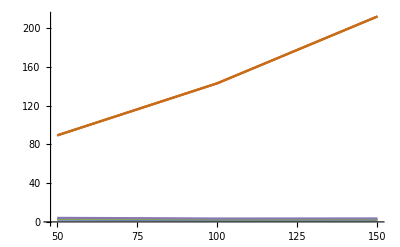

```mathematica
ListPlot[Table[g[i, data4], {i, 3, 8}], Joined->True]
```

## Mode Performances vs δT (ms) 75x75

```mathematica
δt ={"0.001","0.002","0.003","0.004","0.005","0.006","0.007","0.008","0.009","0.010","0.011","0.012","0.013","0.014","0.015","0.016","0.017","0.018","0.019","0.020","0.021","0.022","0.023","0.024","0.025","0.026","0.027","0.028","0.029","0.030","0.040","0.050","0.060","0.070","0.080","0.090","0.100","0.150","0.200","0.250","0.300","0.350","0.400","0.500","0.600","0.700","0.800","0.900","1.000","1.100","1.200","1.300","1.400","1.500","1.600","1.700","1.800","1.900","2.000","2.500","3.000","3.500","4.000","4.500","5.000"};
```

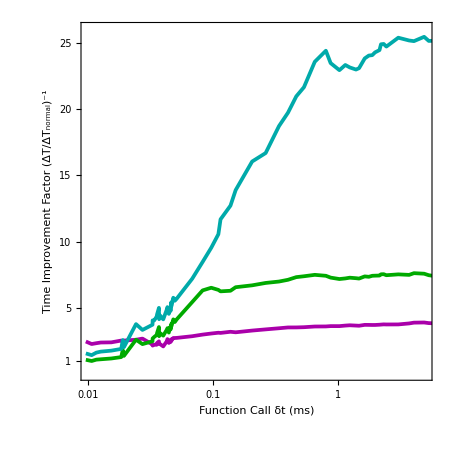

```mathematica
x75=Table[Import[FileNameJoin[{NotebookDirectory[],"Multi_Runs/75x75/4_Comparison_"<>ToString[i]<>".dat"}], "CSV"],{i, 1, 9}]//Mean;
result75 = Table[Table[{RealTvsSleepT[[i]],((x75[[i+j*Length[δt]]][[3]])/(x75[[i]][[3]]))^-1}, {i, 1,Length[δt]}], {j, 1,3}];
newResult75 = Table[Sort[result75[[i]],#1[[1]]<#2[[1]]&], {i, 1,Length[result]}];
plot75=ListLogLinearPlot[newResult75, 
FrameLabel->{{"Time Improvement Factor (ΔT/ΔT_normal)^-1",Rotate["Grid: 75×75",π]},{"Function Call δt (ms)","Mode Comparison (9 Runs)"}},
PlotStyle->{ 
 { Thickness[.006],Darker[Magenta],Opacity[1]},
 { Thickness[.006],Darker[Green],Opacity[1]},
 { Thickness[.006],Darker[Cyan],Opacity[1]}},
Frame->True,
PlotRange->{{10^-2,5},{0.1,26}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True, 
LabelStyle->{Background-> White},
FrameStyle->Directive[Black],
FrameTicks->{ {  {{1,"1"},{5,"5"}, {10,"10"}, {15,"15"}, {20,"20"}, {25,"25"}},
None},{{{10^-3,"10^-3"},{10^-2,"10^-2"}, {10^-1,"0.1"}, {0.5,"0.5"}, {1,"1"}, {2,"2"},{3,"3"},{4,"4"}, {5,"5"}},None}},
GridLines->{{0.01, 0.02, 0.03,0.04, 0.05,0.06, 0.07, 0.08, 0.09,{0.1, Dashed}, 0.2, 0.3,0.4, 0.5, 0.6, 0.7, 0.8, 0.9,{1, Dashed},2, 3, 4, 5},{ {1,Dashed}, 2, 3, 4, {5,Dashed}, 6, 7, 8,9, {10, Dashed}, 11, 12, 13, 14, {15, Dashed}, 16, 17, 18, 19,{ 20, Dashed}, 21, 22, 23, 24, {25, Dashed}, 26 }},
GridLinesStyle->Directive[Dotted, Opacity[0.2]],
ImageSize->450,
Background->White,
AspectRatio->1]
```

```mathematica
Export["Mode_Comparison_(75x75).pdf",plot75, "PDF"];
```

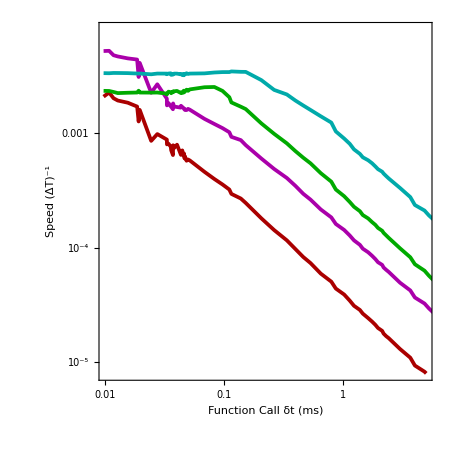

```mathematica
abstime75 = Table[Table[{RealTvsSleepT[[i]],(x75[[i+j*Length[δt]]][[3]])^-1}, {i, 1,Length[δt]}], {j, 0,3}];
abstimeNew75 = Table[Sort[abstime75[[i]],#1[[1]]<#2[[1]]&], {i, 1,Length[abstime75]}];
plot75abstime=ListLogLogPlot[abstimeNew75, 
FrameLabel->{{"Speed (ΔT)^-1",Rotate["Grid: 75×75",π]},{"Function Call δt (ms)","Mode Comparison (9 Runs)"}},
PlotStyle->{ 
{ Thickness[.006],Darker[Red],Opacity[1]},
 { Thickness[.006],Darker[Magenta],Opacity[1]},
 { Thickness[.006],Darker[Green],Opacity[1]},
 { Thickness[.006],Darker[Cyan],Opacity[1]}},
Frame->True,
PlotRange->{{10^-2,5},{8 10^-6,8 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True, 
LabelStyle->{Background-> White},
FrameStyle->Directive[Black],
FrameTicks->{ {  {{10^-5,"10^-5"},{10^-4,"10^-4"}, {10^-3,"10^-3"}},
None},{{{10^-3,"10^-3"},{10^-2,"10^-2"}, {10^-1,"0.1"}, {0.5,"0.5"}, {1,"1"}, {2,"2"},{3,"3"},{4,"4"}, {5,"5"}},None}},
GridLines->{{0.01, 0.02, 0.03,0.04, 0.05,0.06, 0.07, 0.08, 0.09,{0.1, Dashed}, 0.2, 0.3,0.4, 0.5, 0.6, 0.7, 0.8, 0.9,{1, Dashed},2, 3, 4, 5},{  2 10^-6, 3 10^-6, 4 10^-6, 5 10^-6, 6 10^-6, 7 10^-6, 8 10^-6,9 10^-6,{10^-5,Dashed}, 2 10^-5, 3 10^-5, 4 10^-5, 5 10^-5, 6 10^-5, 7 10^-5, 8 10^-5,9 10^-5, {10^-4,Dashed}, 2 10^-4, 3 10^-4, 4 10^-4,5 10^-4, 6 10^-4, 7 10^-4, 8 10^-4,9 10^-4, {10^-3, Dashed}}},
GridLinesStyle->Directive[Dotted, Opacity[0.2]],
ImageSize->450,
Background->White,
AspectRatio->1]
```

## Mode Performances vs δT (ms) 200x200

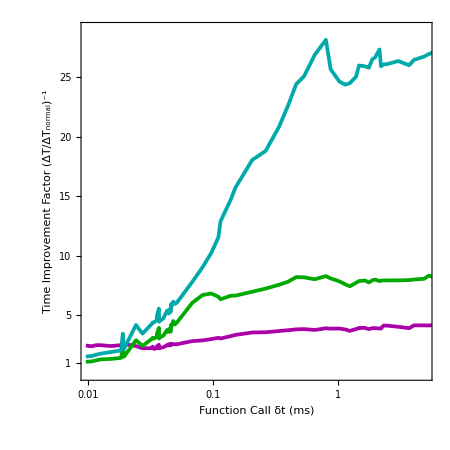

```mathematica
x200=Table[Import[FileNameJoin[{NotebookDirectory[],"Multi_Runs/200x200/4_Comparison_"<>ToString[i]<>".dat"}], "CSV"],{i, 1, 3}]//Mean;
result200 = Table[Table[{RealTvsSleepT[[i]],((x200[[i+j*Length[δt]]][[3]])/(x200[[i]][[3]]))^-1}, {i, 1,Length[δt]}], {j, 1,3}];
newResult200 = Table[Sort[result200[[i]],#1[[1]]<#2[[1]]&], {i, 1,Length[result200]}];
plot200=ListLogLinearPlot[newResult200, 
FrameLabel->{{"Time Improvement Factor (ΔT/ΔT_normal)^-1",Rotate["Grid: 200×200",π]},{"Function Call δt (ms)","Mode Comparison (3 Runs)"}},
PlotStyle->{ 
 { Thickness[.006],Darker[Magenta],Opacity[1]},
 { Thickness[.006],Darker[Green],Opacity[1]},
 { Thickness[.006],Darker[Cyan],Opacity[1]}},
Frame->True,
PlotRange->{{10^-2,5},{0.1,29}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True, 
LabelStyle->{Background-> White},
FrameStyle->Directive[Black],
FrameTicks->{ {  {{1,"1"},{5,"5"}, {10,"10"}, {15,"15"}, {20,"20"}, {25,"25"}},
None},{{{10^-3,"10^-3"},{10^-2,"10^-2"}, {10^-1,"0.1"}, {0.5,"0.5"}, {1,"1"}, {2,"2"},{3,"3"},{4,"4"}, {5,"5"}},None}},
GridLines->{{0.01, 0.02, 0.03,0.04, 0.05,0.06, 0.07, 0.08, 0.09,{0.1, Dashed}, 0.2, 0.3,0.4, 0.5, 0.6, 0.7, 0.8, 0.9,{1, Dashed},2, 3, 4, 5},{ {1,Dashed}, 2, 3, 4, {5,Dashed}, 6, 7, 8,9, {10, Dashed}, 11, 12, 13, 14, {15, Dashed}, 16, 17, 18, 19,{ 20, Dashed}, 21, 22, 23, 24, {25, Dashed}, 26, 27, 28, 29 }},
GridLinesStyle->Directive[Dotted, Opacity[0.2]],
ImageSize->450,
Background->White,
AspectRatio->1]
```

```mathematica
Export["Mode_Comparison_(200x200).pdf",plot200, "PDF"];
```

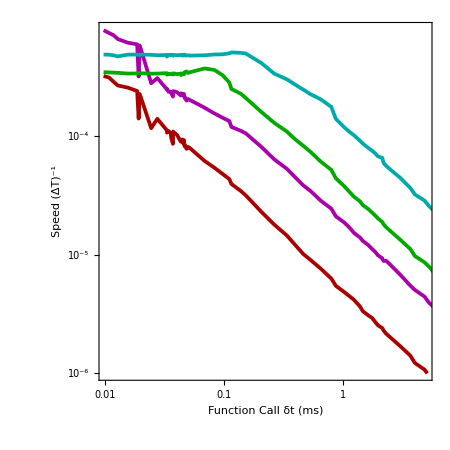

```mathematica
abstime200 = Table[Table[{RealTvsSleepT[[i]],(x200[[i+j*Length[δt]]][[3]])^-1}, {i, 1,Length[δt]}], {j, 0,3}];
abstimeNew200 = Table[Sort[abstime200[[i]],#1[[1]]<#2[[1]]&], {i, 1,Length[abstime200]}];
plot200abstime=ListLogLogPlot[abstimeNew200, 
FrameLabel->{{"Speed (ΔT)^-1",Rotate["Grid: 200×200",π]},{"Function Call δt (ms)","Mode Comparison (3 Runs)"}},
PlotStyle->{ 
{ Thickness[.006],Darker[Red],Opacity[1]},
 { Thickness[.006],Darker[Magenta],Opacity[1]},
 { Thickness[.006],Darker[Green],Opacity[1]},
 { Thickness[.006],Darker[Cyan],Opacity[1]}},
Frame->True,
PlotRange->{{10^-2,5},{10^-6,8 10^-4}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True, 
LabelStyle->{Background-> White},
FrameStyle->Directive[Black],
FrameTicks->{ {  {{10^-5,"10^-5"},{10^-4,"10^-4"}, {10^-3,"10^-3"}},
None},{{{10^-3,"10^-3"},{10^-2,"10^-2"}, {10^-1,"0.1"}, {0.5,"0.5"}, {1,"1"}, {2,"2"},{3,"3"},{4,"4"}, {5,"5"}},None}},
GridLines->{{0.01, 0.02, 0.03,0.04, 0.05,0.06, 0.07, 0.08, 0.09,{0.1, Dashed}, 0.2, 0.3,0.4, 0.5, 0.6, 0.7, 0.8, 0.9,{1, Dashed},2, 3, 4, 5},{  2 10^-6, 3 10^-6, 4 10^-6, 5 10^-6, 6 10^-6, 7 10^-6, 8 10^-6,9 10^-6,{10^-5,Dashed}, 2 10^-5, 3 10^-5, 4 10^-5, 5 10^-5, 6 10^-5, 7 10^-5, 8 10^-5,9 10^-5, {10^-4,Dashed}, 2 10^-4, 3 10^-4, 4 10^-4,5 10^-4, 6 10^-4, 7 10^-4, 8 10^-4,9 10^-4, {10^-3, Dashed}}},
GridLinesStyle->Directive[Dotted, Opacity[0.2]],
ImageSize->450,
Background->White,
AspectRatio->1]
```

## Mode Performances vs δT (ms) 30x30

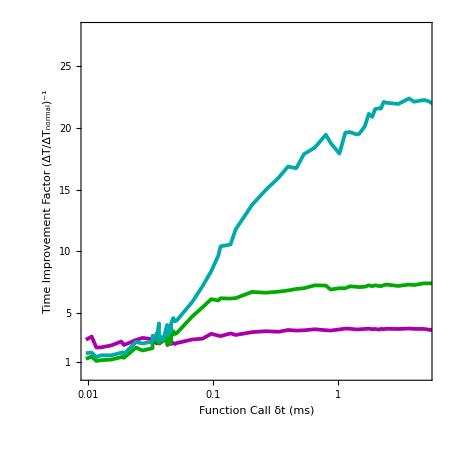

```mathematica
x30=Table[Import[FileNameJoin[{NotebookDirectory[],"Multi_Runs/30x30/4_Comparison_"<>ToString[i]<>".dat"}], "CSV"],{i, 1, 5}]//Mean;
result30 = Table[Table[{RealTvsSleepT[[i]],((x30[[i+j*Length[δt]]][[3]])/(x30[[i]][[3]]))^-1}, {i, 1,Length[δt]}], {j, 1,3}];
newResult30 = Table[Sort[result30[[i]],#1[[1]]<#2[[1]]&], {i, 1,Length[result30]}];
plot30=ListLogLinearPlot[newResult30, 
FrameLabel->{{"Time Improvement Factor (ΔT/ΔT_normal)^-1",Rotate["Grid: 30×30",π]},{"Function Call δt (ms)","Mode Comparison (3 Runs)"}},
PlotStyle->{ 
 { Thickness[.006],Darker[Magenta],Opacity[1]},
 { Thickness[.006],Darker[Green],Opacity[1]},
 { Thickness[.006],Darker[Cyan],Opacity[1]}},
Frame->True,
PlotRange->{{10^-2,5},{0.1,28}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True, 
LabelStyle->{Background-> White},
FrameStyle->Directive[Black],
FrameTicks->{ {  {{1,"1"},{5,"5"}, {10,"10"}, {15,"15"}, {20,"20"}, {25,"25"}},
None},{{{10^-3,"10^-3"},{10^-2,"10^-2"}, {10^-1,"0.1"}, {0.5,"0.5"}, {1,"1"}, {2,"2"},{3,"3"},{4,"4"}, {5,"5"}},None}},
GridLines->{{0.01, 0.02, 0.03,0.04, 0.05,0.06, 0.07, 0.08, 0.09,{0.1, Dashed}, 0.2, 0.3,0.4, 0.5, 0.6, 0.7, 0.8, 0.9,{1, Dashed},2, 3, 4, 5},{ {1,Dashed}, 2, 3, 4, {5,Dashed}, 6, 7, 8,9, {10, Dashed}, 11, 12, 13, 14, {15, Dashed}, 16, 17, 18, 19,{ 20, Dashed}, 21, 22, 23, 24, {25, Dashed}, 26, 27, 28, 29 }},
GridLinesStyle->Directive[Dotted, Opacity[0.2]],
ImageSize->450,
Background->White,
AspectRatio->1]
```

```mathematica
Export["Mode_Comparison_(30x30).pdf",plot30, "PDF"];
```

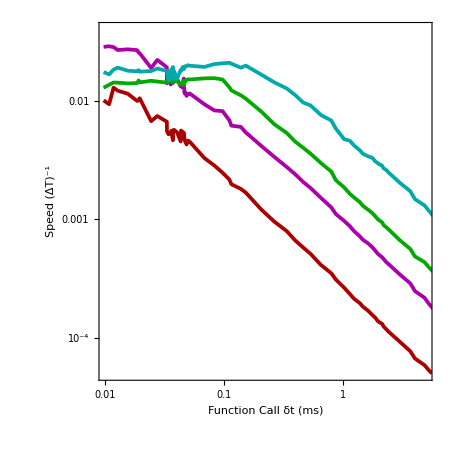

```mathematica
abstime30 = Table[Table[{RealTvsSleepT[[i]],(x30[[i+j*Length[δt]]][[3]])^-1}, {i, 1,Length[δt]}], {j, 0,3}];
abstimeNew30 = Table[Sort[abstime30[[i]],#1[[1]]<#2[[1]]&], {i, 1,Length[abstime30]}];
plot30abstime=ListLogLogPlot[abstimeNew30, 
FrameLabel->{{"Speed (ΔT)^-1",Rotate["Grid: 30×30",π]},{"Function Call δt (ms)","Mode Comparison (5 Runs)"}},
PlotStyle->{ 
{ Thickness[.006],Darker[Red],Opacity[1]},
 { Thickness[.006],Darker[Magenta],Opacity[1]},
 { Thickness[.006],Darker[Green],Opacity[1]},
 { Thickness[.006],Darker[Cyan],Opacity[1]}},
Frame->True,
PlotRange->{{10^-2,5},{5 10^-5,4 10^-2}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Joined->True, 
LabelStyle->{Background-> White},
FrameStyle->Directive[Black],
FrameTicks->{ {  {{10^-2,"10^-2"},{10^-4,"10^-4"}, {10^-3,"10^-3"}},
None},{{{10^-3,"10^-3"},{10^-2,"10^-2"}, {10^-1,"0.1"}, {0.5,"0.5"}, {1,"1"}, {2,"2"},{3,"3"},{4,"4"}, {5,"5"}},None}},
GridLines->{{0.01, 0.02, 0.03,0.04, 0.05,0.06, 0.07, 0.08, 0.09,{0.1, Dashed}, 0.2, 0.3,0.4, 0.5, 0.6, 0.7, 0.8, 0.9,{1, Dashed},2, 3, 4, 5},{  {10^-5,Dashed}, 2 10^-5, 3 10^-5, 4 10^-5, 5 10^-5, 6 10^-5, 7 10^-5, 8 10^-5,9 10^-5, {10^-4,Dashed}, 2 10^-4, 3 10^-4, 4 10^-4,5 10^-4, 6 10^-4, 7 10^-4, 8 10^-4,9 10^-4, {10^-3, Dashed}, 2 10^-3, 3 10^-3, 4 10^-3, 5 10^-3, 6 10^-3, 7 10^-3, 8 10^-3,9 10^-3,{10^-2, Dashed}, 2 10^-2, 3 10^-2, 4 10^-2}},
GridLinesStyle->Directive[Dotted, Opacity[0.2]],
ImageSize->450,
Background->White,
AspectRatio->1]
```